## Quantity/Unit Convenience

### UnitForm: Postfix friendly UnitConvert

```mathematica
UnitForm[units_][quantity_]:=UnitConvert[quantity,units]
UnitForm::usage="like UnitConvert but for postfix";
```

```mathematica
(* Make it so you can always UnitForm 0 into any units *)
(*UnitConvert[zero_?(#==0&),targetunit_]^:=Quantity[0,targetunit]*)
(*UnitConvert[0.,targetunit_]^:=Quantity[0,targetunit]*)
```

#### Example usage

```mathematica
Quantity[10,"Meters/Second"]//N@*UnitForm["mph"]
```

22.3694 mi/h

### ("unit")_q: Interpret a string as a quantity with subscript q

```mathematica
Subscript[s_String, q]:=Quantity[s]
```

#### Example usage

```mathematica
10 Subscript["mph", q]
```

10 mi/h

### loadQuantities: Load common physical quantities, both into the input of the function and globally

```mathematica
ClearAll@loadQuantities;
quantityAssoc[HoldPattern@symb]:=<|ℏ->Quantity["ReducedPlanckConstant"]|>[symb]
(* Makes loadQuantities idempotent, so loadQuantities[loadQuantities[ℏ]]==loadQuantities[ℏ] *)
loadQuantities[q_Quantity]:=q;
(* Define constants that can be loaded *)
loadQuantities[HoldPattern@ℏ]:=ℏ=Quantity["ReducedPlanckConstant"];
loadQuantities[HoldPattern[h]]:=h=Quantity["PlanckConstant"];
loadQuantities[HoldPattern@c]:=c=Quantity["SpeedOfLight"];
loadQuantities[HoldPattern@Subscript[q, e]]:=Subscript[q, e]=Quantity["ElectronCharge"];
loadQuantities[HoldPattern@Subscript[m, e]]:=Subscript[m, e]=Quantity["ElectronMass"];
loadQuantities[HoldPattern@Subscript[m, p]]:=Subscript[m, p]=Quantity["ProtonMass"];
loadQuantities[HoldPattern@Subscript[m, n]]:=Subscript[m, n]=Quantity["NeutronMass"];
loadQuantities[HoldPattern@Subscript[m, μ]]:=Subscript[m, μ]=Quantity["MuonMass"];
loadQuantities[HoldPattern@Subscript[m, τ]]:=Subscript[m, τ]=Quantity["TauMass"];
loadQuantities[HoldPattern@Subscript[ϵ, 0]]:=Subscript[ϵ, 0]=Quantity["VacuumPermittivity"];
loadQuantities[HoldPattern@Subscript[μ, 0]]:=Subscript[μ, 0]=Quantity["VacuumPermeability"];
loadQuantities[HoldPattern@Subscript[a, 0]]:=Subscript[a, 0]=Quantity["BohrRadius"];
loadQuantities[HoldPattern@G]:=G=Quantity["GravitationalConstant"];
loadQuantities[HoldPattern@Subscript[N, A]]:=Subscript[N, A]=Quantity["AvogadroConstant"];
loadQuantities[HoldPattern@Subscript[k, B]]:=Subscript[k, B]=Quantity["BoltzmannConstant"];
(* Allow list of quantities to be loaded  *)
SetAttributes[loadQuantities,Listable]
(*(* Handle other symbols not defined above, and return 0 *)
loadQuantities::unknownSymb="Unknown symbol `1`";
loadQuantities[symb_]:=(Message[loadQuantities::unknownSymb,symb];symb);*)
(* Return unknown symbols unchanged *)
loadQuantities[symb_]:=symb;
(* Load product, sum, etc of constants at once *)
loadQuantities[HoldPattern[f_[symbs__]]]:=f@@loadQuantities[{symbs}]
(* Allow list of quantities to be loaded without surrounding in brackets *)
loadQuantities[symbs__]:=loadQuantities[{symbs}]
(* With no arguments, load all quantities *)
(* todo figure out how to not have to hardcode the -5 (# of non-definition defs) *)
loadQuantities[]:=(Keys[DownValues[loadQuantities]]/.loadQuantities->List)[[;;-5,1]]//Flatten//ReleaseHold//loadQuantities
```

#### Example usage:

Load some quantities, then use them

```mathematica
loadQuantities[Subscript[μ, 0],Subscript[q, e],ℏ,Subscript[m, e],Subscript[a, 0]]
(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)//UnitForm@"Teslas"
Subscript[μ, 0]=.
Subscript[q, e]=.
ℏ=.
Subscript[m, e]=.
Subscript[a, 0]=.
```

{ μ_0, e, ℏ, m_e, a_0}

12.516824 T

Load needed quantities in an expression, and then re-use them

```mathematica
loadQuantities[(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)]//UnitForm@"Teslas"
Subscript[m, e] loadQuantities[c^2]//UnitForm@"keV"
Subscript[μ, 0]=.
Subscript[q, e]=.
ℏ=.
Subscript[m, e]=.
Subscript[a, 0]=.
c=.
```

12.516824 T

510.99895 keV

Load all quantities, then use them

```mathematica
loadQuantities[]
(Subscript[μ, 0] Subscript[q, e] ℏ)/(4π Subscript[m, e] Subscript[a, 0]^3)
```

{ c, G, h, ℏ, a_0, k, m_e, m_n, m_p, m_μ, m_τ, N_A, e, ε_0, μ_0}

1/(4 π) e μ_0 ℏ/(m_e a_0^3)

## Side Effects

Useful when you want to keep the value of some expression, but also do something else with it (print it, save it, etc)

### also: Do something as a side effect

```mathematica
also[f_][x_]:=(f@x;x)
```

#### Example usage:

```mathematica
x={2}
y=RandomInteger[10]//also[AppendTo[x,#]&]
x
```

{2}

8

{2,8}

### alsoPrint: Print some thing as a side effect

```mathematica
alsoPrint[f_:Identity]:=also[Print@*f]
```

#### Example usage:

```mathematica
A=RandomInteger[10,{4,4}]//alsoPrint@MatrixForm;
N@Eigenvalues@A
```

(5 | 4 | 10 | 10
6 | 9 | 10 | 6
4 | 4 | 2 | 3
5 | 7 | 2 | 9)

{23.9211,-4.00935,2.54412+1.76634 ⅈ,2.54412-1.76634 ⅈ}

### save, alsoSave: Save a figure as png or svg (as a side effect)

```mathematica
saveDirectory[]:=Module[
	{dir=FileNameJoin@{NotebookDirectory[],"mathematica_figures"}},
	If[
		!DirectoryQ@dir,
		CreateDirectory[FileNameJoin@{NotebookDirectory[],"mathematica_figures"}],
		dir
	]
]
save[fig_,name_String,format_String:"pdf",dpi_Integer:500]:=Export[FileNameJoin@{saveDirectory[],name<>"."<>format},fig,ImageResolution->dpi]
save[fig_,name_String,formats_List,dpi_Integer:500]:=save[fig,name,#,dpi]&/@formats
alsoSave[name_String,format_String:"pdf",dpi_Integer:500]:=also[save[#,name,format,dpi]&]
alsoSave[name_String,formats_List,dpi_Integer:500]:=also[save[#,name,formats,dpi]&]
```

### alsoCopy:

```mathematica
alsoCopyOpts[opts___]:=also[CopyToClipboard@Rasterize[#,opts]&];
alsoCopy=alsoCopyOpts[]
```

also[CopyToClipboard[Rasterize[#1]]&]

### tableHeaded: TableForm but with headers

```mathematica
tableHeaded[headers_][list_]:=TableForm[list,TableHeadings->headers]
tableHeadedRows[rows_][list_]:=TableForm[list,TableHeadings->{rows,None}]
tableHeadedCols[cols_][list_]:=TableForm[list,TableHeadings->{None,cols}]
```

```mathematica
a=RandomInteger[5,4];
b=RandomInteger[10,6];
{a,b}//tableHeadedRows[{"a","b"}]
```

a | 4 | 0 | 3 | 5 |  | 
b | 1 | 2 | 10 | 0 | 4 | 2

## Colors

### defaultColorData: Quicker access to the default plot colors

```mathematica
defaultColorData[]:=ColorData[97]
defaultColorData[n_Integer]:=defaultColorData[][n]
```

#### Example usage:

When combining separate plots with Show, this makes it easier to use the right two colors

```mathematica
f=x^2;
data=Table[{x,f+RandomReal[0.5]},{x,0,2,0.2}];
```

```mathematica
plot=Plot[
f,{x,0,2}
];
```

By default, both are this blue color (ColorData[97][1])

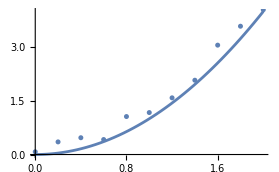

```mathematica
Show[
plot,ListPlot[data]
]
```

To get the same different color as if both were in the same Plot function:

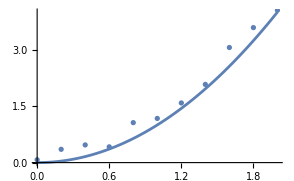

```mathematica
Show[
plot,ListPlot[data,ColorFunction->(defaultColorData[2]&)]
]
```

### Pride Colors!

```mathematica
(* Pride Flags! *)
(* How to add gradients: https://mathematica.stackexchange.com/questions/57885/is-it-possible-to-insert-new-colour-schemes-into-colordata/57893#57893 *)
(* Flag rgb colors: https://www.flagcolorcodes.com/flags/pride *)

ColorData[1];
(* Export this function so users can add gradients as needed *)
insertGradient[name_,gradColors_]:=If[
	!MemberQ[ColorData["Gradients"],name],
	(
		AppendTo[
			DataPaclets`ColorDataDump`colorSchemes,
			{{name,"",{}},{"Gradients"},1,{0,1},gradColors,""}
		];
		AppendTo[
			DataPaclets`ColorDataDump`colorSchemeNames,
			name
		];
	)
]
Module[{data,names,colors},
	data=Import["https://raw.githubusercontent.com/Annie-Schwartz/YouTilities/master/flags.tsv","TSV","Numeric"->False];
	names=#<>"Flag"&/@data[[;;,1]];
	colors=Map[RGBColor["#"<>#]&,data[[;;,2;;]],{2}];
	
	insertGradient@@#&/@Transpose@{names,colors};
]
```

#### List of Gradients:

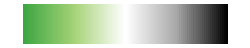
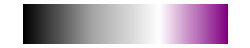
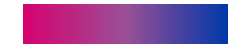
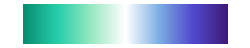
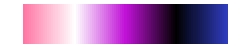
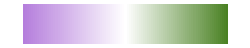
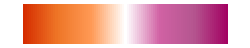
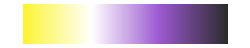
AromanticFlag | -Graphics-
AsexualFlag | -Graphics-
BiFlag | -Graphics-
GayFlag | -Graphics-
GenderfluidFlag | -Graphics-
GenderqueerFlag | -Graphics-
LesbianFlag | -Graphics-
NonbinaryFlag | -Graphics-
NWAromanticFlag | -Graphics-
NWAsexualFlag | -Graphics-
NWGayFlag | -Graphics-
NWGenderfluidFlag | -Graphics-
NWGenderqueerFlag | -Graphics-
NWLesbianFlag | -Graphics-
NWNonbinaryFlag | -Graphics-
NWTransFlag | -Graphics-
OmniFlag | -Graphics-
PanFlag | -Graphics-
PrideFlag | -Graphics-
TransFlag | -Graphics-

```mathematica
With[{data=Select[StringEndsQ@"Flag"]@ColorData@"Gradients"},
TableForm[
ColorData[#,"Image"]&/@data,
TableHeadings->{data,None}
]
]
```

#### Example usage:

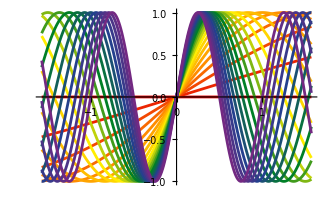

```mathematica
Table[Sin[n π x],{n,0,2,0.1}];
Plot[
%,
{x,-π/2,π/2},
PlotStyle->"PrideFlag"
]
```

## Linear Algebra

### EigvecsT, EigsysT: Wrapper for melt’s functions to allow for getting the eigenvectors as lists of lists, rather than a matrix (row-major vs col-major)

```mathematica
Thread[f[{a,b},{c,d}]]
```

{f[a,c],f[b,d]}

```mathematica
EigvecsT[A_,neigs_:"all",Δ_:Automatic]:=Transpose@Eigvecs[A,neigs,Δ]
EigsysT[A_,neigs_:"all",Δ_:Automatic]:=MapThread[#1@#2&,{{Identity,Transpose},Eigsys[A,neigs,Δ]}]
```

#### Example Usage:

```mathematica
<<http://www.fmt.if.usp.br/~gtlandi/download/melt.m
(* Eigenvalues of a spin 3/2 Hamiltonian *)
LoadArbitrarySpinMatrices[3/2];
H = Sz + 0.3 Sx.Sx//mf;
```

(1.725 | 0 | 0.259808 | 0
0 | 1.025 | 0 | 0.259808
0.259808 | 0 | 0.025 | 0
0 | 0.259808 | 0 | -1.275)

```mathematica
eigenStuff[H]
```

λ | Eigenvector
1.76382 | (0.989021
0.
0.147776
0.)
-1.30398 | (0.
-0.110866
0.
0.993835)
1.05398 | (0.
-0.993835
0.
-0.110866)
-0.0138194 | (0.147776
0.
-0.989021
0.)

```mathematica
EigsysT@H
```

{{-1.30398,-0.0138194,1.05398,1.76382},{{0.,-0.110866,0.,0.993835},{0.147776,0.,-0.989021,0.},{0.,-0.993835,0.,-0.110866},{0.989021,0.,0.147776,0.}}}

```mathematica
eigenStuff[H,sys->EigsysT]
```

λ | Eigenvector
-1.30398 | (0.
-0.110866
0.
0.993835)
-0.0138194 | (0.147776
0.
-0.989021
0.)
1.05398 | (0.
-0.993835
0.
-0.110866)
1.76382 | (0.989021
0.
0.147776
0.)

```mathematica
EigvecsT[H]//tableHeadedCols[{"v_1","v_2","v_3","v_4"}]
```

v_1 | v_2 | v_3 | v_4
0. | -0.110866 | 0. | 0.993835
0.147776 | 0. | -0.989021 | 0.
0. | -0.993835 | 0. | -0.110866
0.989021 | 0. | 0.147776 | 0.

### M_mp^n: Exponentiate matrices with correct matrix multiplication

Todo: make a more general version that works with kron too I think makes the most sense

```mathematica
(* Exponentiate with something other than Times (useful for matrix powers with Dot) *)
Subscript/:Power[Subscript[mat_,mp],n_]:=MatrixPower[mat,n]
Subscript/:Power[Subscript[mat_,Dot],n_]:=MatrixPower[mat,n]
```

#### Example usage:

```mathematica
A=PauliMatrix[1]//alsoPrint@MatrixForm;
```

(0 | 1
1 | 0)

The normal exponentiation behavior is to multiply element-wise

```mathematica
Table[MatrixForm[A^n],{n,3}]
```

{(0 | 1
1 | 0),(0 | 1
1 | 0),(0 | 1
1 | 0)}

Using this gets the correct matrix multiplication n times

```mathematica
Table[MatrixForm[Subscript[A, mp]^n],{n,3}]
```

{(0 | 1
1 | 0),(1 | 0
0 | 1),(0 | 1
1 | 0)}

Another common use case, with melt’s kron function

```mathematica
Subscript/:Power[Subscript[mat_,f_],n_Integer]:=f@@Table[mat,n]/;(Print[DownValues@f];False)
```

```mathematica
kron[mats__]:=KroneckerProduct[mats];
CircleTimes[things__]:=kron[things];
```

```mathematica
Definition[Dot]
```

Attributes[Dot]={Flat,OneIdentity,Protected}

```mathematica
<<https://raw.githubusercontent.com/szhorvat/Spelunking/master/Spelunking.m
```

```mathematica
Spelunk[Dot]
```

Attributes[Dot]={Flat,OneIdentity}

```mathematica
Subscript[A, Dot]^2
```

{{1,0},{0,1}}

```mathematica
Dimensions[Subscript[A, kron]^2]
```

{2}

### eigenStuff: Make a nice lil table of eigenvalues & vectors

matrix: The matrix to calculate the eigenvalues & vectors for
sys: The function used to get the eigens. Must return a tuple of {vals,vecs} Defaults to Eigensystem, but is configurable (mostly for use with melt’s Eigsys for sorting)
aiλ: Whether to show a column for A-Iλ
rref: Whether to show a column for the reduced row echelon form
normalize: Whether to normalize the eigenvectors

```mathematica
ClearAll@eigenStuff
eigenStuff::zeroEigenvectors="Some zero-eigenvectors";
eigenStuff::unequal="#vals!=#vecs";
eigenStuff[matrix_,opts:OptionsPattern[{sys->Eigensystem,aiλ->False,rref->False,normalize->False}]]:=Module[
	{
		aiλ=OptionValue@aiλ,
		rref=OptionValue@rref,
		normalize=OptionValue@normalize,
		sys=OptionValue@sys,
		len=Length@matrix,
		vecs,vals
	},
	{vals,vecs}=sys[matrix];
	vecs=If[normalize,Normalize/@vecs,vecs];
	If[ContainsAny[vecs,{Table[0,len]}],
		Throw[Message[eigenStuff::zeroEigenvectors]]
	];
	AIλ=matrix-# IdentityMatrix@len&/@vals//Simplify;
	If[Length/@{vals,vecs}/.List->Equal,
		Grid[
			Join[
				{{"λ",If[aiλ,"A-Iλ",Nothing],If[rref,"RREF",Nothing],"Eigenvector"}},
				{
					vals,
					If[aiλ,MatrixForm/@AIλ,Nothing],
					If[rref,MatrixForm@*RowReduce/@AIλ,Nothing],
					MatrixForm/@vecs
				}ᵀ
			],
			Frame->All
		],
		Message[eigenStuff::unequal]
	]
]
```

```mathematica
A=RandomInteger[10,{4,4}];
```

```mathematica
eigenStuff[A,rref->False,aiλ->False,normalize->True,sys->Eigsys]//N
```

λ | Eigenvector
-7.04733 | (-0.775882
0.0941402
-0.334806
-0.526355)
-2.64597 | (0.249192
0.36187
0.569483
-0.694725)
4.47617 | (0.328695
-0.729094
0.463801
-0.381144)
19.2171 | (0.509951
0.233938
-0.650125
-0.512407)

### hc (and cc): Add the Hermitian (complex) conjugate of a matrix (value) to itself

```mathematica
CirclePlus[mat_?MatrixQ,hc]:=mat+mat†
CirclePlus[val_,cc]:=val+val*
```

```mathematica
mat={{1, 0, 2}, {0, 1, 0}, {0, 0, 0}};
mat+mat†//MatrixForm
mat⊕hc//MatrixForm
```

(2 | 0 | 2
0 | 2 | 0
2 | 0 | 0)

(2 | 0 | 2
0 | 2 | 0
2 | 0 | 0)

### LoadBra: Defines Bra as the complex conjugate of Ket of the same things

```mathematica
LoadBra[]:=(
labels__:=labels*;
a__b__:=a*.b;
)
```

#### Example usage:

```mathematica
n_:={n,ⅈ,n+ⅈ}
2
2
```

{2,ⅈ,2+ⅈ}

{2,-ⅈ,2-ⅈ}

```mathematica
LoadBra[]
2
2
22
```

{2,ⅈ,2+ⅈ}

{2,-ⅈ,2-ⅈ}

6+4 ⅈ

### LoadArbitrarySpinMatricesJ: Melt’s LoadArbitrarySpinMatrices but defining Jx, etc. instead of Sx

```mathematica
?LoadArbitrarySpinMatrices
```

```mathematica
LoadArbitrarySpinMatricesJ[S_,type_:"n",chain_:1]:=If[Length@DownValues@LoadArbitrarySpinMatrices==0,
"Please make sure to load Melt before running LoadArbitrarySpinMatricesJ!",
(*{J0,Jx,Jy,Jz,Jp,Jm,𝒥x,𝒥y,𝒥z,𝒥p,𝒥m}=Eat[{S0,Sx,Sy,Sz,Sp,Sm,𝒮x,𝒮y,𝒮z,𝒮p,𝒮m},LoadArbitrarySpinMatrices[S,type,chain]];*)
Block[{S0,Sx,Sy,Sz,Sp,Sm,𝒮x,𝒮y,𝒮z,𝒮p,𝒮m},
ClearAll[J0,Jx,Jy,Jz,Jp,Jm];
LoadArbitrarySpinMatrices[S,type,chain];
J0=S0;Jx=Sx;Jy=Sy;Jz=Sz;Jp=Sp;Jm=Sm;
If[chain===1,
"Matrices loaded: J0 (=1), Jx, Jy, Jz, Jp, Jm",
𝒥0=𝒮0;𝒥x=𝒮x;𝒥y=𝒮y;𝒥z=𝒮z;𝒥p=𝒮p;𝒥m=𝒮m;"Matrices loaded: 𝒥0 (=1), 𝒥x, 𝒥y, 𝒥z, 𝒥p, 𝒥m"
]
]
]
```

```mathematica
LoadArbitrarySpinMatricesJ[5]
```

Please make sure to load Melt before running LoadArbitrarySpinMatricesJ

### BlockDiagonalizer: Construct a unitary to block diagonalize according to some symmetry (i.e. operator)

```mathematica
ClearAll[BlockDiagonalizer]
BlockDiagonalizer[ops__]:=Module[{os=Reverse@{ops},U},
U=BlockDiagonalizer@First@os;
Do[
U=U.BlockDiagonalizer[U†.os[[idx]].U],
{idx,2,Length@os}
];
U
]
BlockDiagonalizer[op_]:=LocalizeAll[{},{},
{λs,vs}=Eigensystem@op;
evals=Sort[DeleteDuplicates@λs,Greater];
Transpose@flat1@Table[
Normalize/@vs[[Flatten@Position[λs,λ]]],
{λ,evals}
]
]
```

#### Example Usage

The following model of two coupled spins:

```mathematica
LoadArbitrarySpinMatricesJ[j=1,"a"];
𝒥0=J0⊗J0;
{𝒥x,𝒥y,𝒥z}=Table[
kron@@Basis[2,idx]/.{1->op,0->J0},
{op,{Jx,Jy,Jz}},
{idx,2}
];
ℋ[x_]:=-x Total@𝒥z-(1-x)/(4j)Subscript[Total[𝒥x], mp]^2
```

conserves parity (Π) and total spin 𝒥2:

```mathematica
Π=MatrixExp[ⅈ π (Jz-j J0)];
𝒥2=Subscript[Total[𝒥x], mp]^2+Subscript[Total[𝒥y], mp]^2+Subscript[Total[𝒥z], mp]^2;
ℂ[ℋ[x],Π⊗Π]//Simplify
Map[Simplify,ℂ[ℋ[x],𝒥2],{2}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Thus, we can find a unitary matrix U that simultaneously (block) diagonalizes ℋ (or anything else that commutes with Π and 𝒥2) into blocks of definite parity and total spin:

```mathematica
U=BlockDiagonalizer[𝒥2,Π⊗Π];
Ui=Inverse@U;
Ui.ℋ[x].U//Simplify
Ui.ℋ[1].U
```

(1/8 (-5-3 x) | 3/8 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/8 (-1+x) | 1/8 (-5+13 x) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 (-1-7 x) | 1/4 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 √(3/2) (-1+x) | 3/4 (-1+x) | 1/4 √(3/2) (-1+x) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 √(3/2) (-1+x) | 1/4 (-1+9 x) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 (-1-7 x) | 1/8 (-1+x) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 (-1+x) | 1/8 (-1+9 x) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (-1+x) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Note that the order of symmetries is important! The above first block diagonalized by total spin, the below first block diagonalizes by parity:

```mathematica
U=BlockDiagonalizer[Π⊗Π,𝒥2];
Ui=Inverse@U;
Ui.ℋ[x].U//Simplify
Ui.ℋ[1].U
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 (-1+x) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 (-1-7 x) | 1/4 √(3/2) (-1+x) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 √(3/2) (-1+x) | 3/4 (-1+x) | 1/4 √(3/2) (-1+x) | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 √(3/2) (-1+x) | 1/4 (-1+9 x) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 (-1-7 x) | 1/8 (-1+x) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 (-1+x) | 1/8 (-1+9 x) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 (-5-3 x) | 3/8 (-1+x)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/8 (-1+x) | 1/8 (-5+13 x))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### BlockEigvals: Diagonalize a block diagonalizable matrix

⚠️ Note that this will give incorrect eigenvalues if the matrix doesn’t commute with each of the symmetry operators.

```mathematica
ClearAll[BlockEigvals]
BlockEigvals[mat_,U_]:=With[{Ui=Inverse@U},
Eigvals[Ui.mat.U]
]
(*BlockEigvals2[mat_,U_]:=With[{Ui=Inverse@U},
Eigvals[BlockDiagonalMatrix[Ui.mat.U]]
]*)
```

```mathematica
LoadLMG[j=2^2];
Chop[Inverse[U[j]].ℋ[h].U[j]]//EchoFunction@MatrixForm;
bd=BlockDiagonalMatrix[%]
```

(-1.25 | -0.592927 | -0.592927 | 0 | 0 | 0 | 0 | 0 | 0
-0.592927 | 1. (-1.-2. h) | 0 | -0.330719 | 0 | 0 | 0 | 0 | 0
-0.592927 | 0 | 1. (-1.+2. h) | 0 | -0.330719 | 0 | 0 | 0 | 0
0 | -0.330719 | 0 | 1. (-0.25-4. h) | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.330719 | 0 | 1. (-0.25+4. h) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. (-1.1875-1. h) | -0.625 | -0.496078 | 0
0 | 0 | 0 | 0 | 0 | -0.625 | 1. (-1.1875+1. h) | 0 | -0.496078
0 | 0 | 0 | 0 | 0 | -0.496078 | 0 | 1. (-0.6875-3. h) | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.496078 | 0 | 1. (-0.6875+3. h))

BlockDiagonalMatrix[…]

```mathematica
<<C:\Users\annie\Documents\Rochester\Research\melt.m
```

```mathematica
ClearAll[U]
Do[LoadLMG[j];U[j]=Quiet@BlockDiagonalizer[Π]//EchoTiming,{j,js}];
```

0.0004155

0.000191

0.0002066

0.000281

0.0007051

0.0049051

0.0157999

0.042549

0.150427

0.600252

```mathematica
fns={Quiet@*Eigvals,Last@*Quiet@*LMGEigen,BlockEigvals[#,U[j]]&};
js=2^Range[10];
ClearAll[j]
timings=Benchmark[fns,js,
j|->(LoadLMG@j;ℋ[1.2])
]
```

00:01:16TimeObject[{0,1,16},Instant]

{{{2,0.00118236},{4,0.0014735},{8,0.00188886},{16,0.00333113},{32,0.00696688},{64,0.024346},{128,0.0791614},{256,0.300665},{512,1.0557},{1024,4.36281}},{{2,0.00145561},{4,0.00180509},{8,0.00252003},{16,0.00331969},{32,0.00730289},{64,0.0209573},{128,0.0800381},{256,0.295694},{512,1.11996},{1024,4.57486}},{{2,0.00117839},{4,0.00145657},{8,0.00217588},{16,0.00281407},{32,0.0062364},{64,0.0173605},{128,0.0603748},{256,0.229256},{512,0.880938},{1024,3.56627}}}

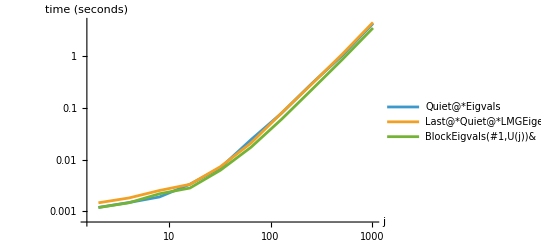

| Quiet@*Eigvals | Last@*Quiet@*LMGEigen | BlockEigvals[#1,U[j]]&
2 | 0.00118236 | 0.00145561 | 0.00117839
4 | 0.0014735 | 0.00180509 | 0.00145657
8 | 0.00188886 | 0.00252003 | 0.00217588
16 | 0.00333113 | 0.00331969 | 0.00281407
32 | 0.00696688 | 0.00730289 | 0.0062364
64 | 0.024346 | 0.0209573 | 0.0173605
128 | 0.0791614 | 0.0800381 | 0.0603748
256 | 0.300665 | 0.295694 | 0.229256
512 | 1.0557 | 1.11996 | 0.880938
1024 | 4.36281 | 4.57486 | 3.56627

```mathematica
ListLogLogPlot[timings,PlotLegends->fns,AxesLabel->{"j","time (seconds)"},PlotRange->All,Joined->True]
timings[[;;,;;,2]]ᵀ//tableHeaded@{js,fns}
```

#### Example Usage:

## Miscellaneous

### PrePrintMatrixForm: Assign to $PrePrint to format matrices automatically

```mathematica
ClearAll[PrePrintMatrixForm]
PrePrintMatrixForm=If[MatrixQ@#,MatrixForm@#,#]&;
```

### Enumerate: Like enumerate in every other language

```mathematica
ClearAll[enumerate]
enumerate=MapIndexed[{#2[[1]],#1}&];
```

### SparseReplaceAll: Like ReplaceAll but works with SparseArrays

```mathematica
(* https://mathematica.stackexchange.com/a/154287 *)
SparseReplaceAll[s_SparseArray,rule_]:=With[{
		elems=ReplaceAll[s["NonzeroValues"],rule],
		default=ReplaceAll[s["Background"],rule]
	},
	SparseArray[
		Automatic,
		s["Dimensions"],
		default,
		{1,{s["RowPointers"],s["ColumnIndices"]},elems}
	]
]
```

#### Example Usage

Say we have a sparse matrix with values μ_i above and below the diagonal:

```mathematica
A=SparseArray[
{
Band[{1,2}]->Array[Subscript[μ, #]&,{3}],
Band[{2,1}]->Array[Subscript[μ, #]&,{3}]
},
{4,4}
]
Eigenvalues[A]
```

SparseArray[…]

{-(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),-(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2)}

And we now have specific values of μ_i we want to use:

```mathematica
rules=Array[Subscript[μ, #]->RandomReal[{-10,10}]&,3]
```

{μ_1→9.24832,μ_2→4.20148,μ_3→-8.43884}

The normal replacement doesn’t work!

```mathematica
A/.rules
ReplaceAll[A,rules] (* equivalent to the above *)
Eigenvalues[%]
```

SparseArray[…]

SparseArray[…]

{-(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2-√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),-(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2),(√(μ_1^2+μ_2^2+μ_3^2+√(-4 μ_1^2 μ_3^2+(-μ_1^2-μ_2^2-μ_3^2)^2)))/(√2)}

So we use SparseReplaceAll instead!

```mathematica
SparseReplaceAll[A,rules]
Eigenvalues[%]
```

SparseArray[…]

{-11.229,11.229,6.95029,-6.95029}

### fMap: Removed, see Comap

### No more laggy/slow chart highlighting!

```mathematica
Charting$InteractiveHighlighting=False;
```

### {list}_seq: Convert a List to a Sequence

```mathematica
Subscript[l_List,seq]:=Sequence@@l
```

#### Example Usage:

```mathematica
f[Subscript[{1,2,3}, seq]]
```

f[1,2,3]

### Benchmark: Compare time taken by different implementations of functions

```mathematica
ClearAll[Benchmark]
Benchmark[fns_List,ns_List,nToInput_]:=Transpose@table[
With[{input=nToInput@n},
Table[{n,RepeatedTiming[fn@nToInput@n][[1]]},{fn,fns}]
],
{n,ns}
]
```

## Strings

### "String with ``"_(sf/st): StringForm/StringTemplate

```mathematica
Subscript[s_String,sf][exprs__]:=StringForm[s,exprs]
Subscript[s_String,st]:=StringTemplate[s]
```

#### Example Usage :

StringForm displays as a string but keeps the StringForm head

```mathematica
Subscript["Hello `` (``)", sf]["World",42]
%//InputForm
```

Hello World (42)

StringForm["Hello `` (``)", "World", 42]

StringTemplate evaluates to a string

```mathematica
Subscript["Hello `` (``)", st]["World",42]
%//FullForm
```

Hello World (42)

"Hello World (42)"

### StringPrepend/StringAppend: Like Prepend/Append, but for Strings.

```mathematica
StringPrepend[rest_,pre_]:=pre<>ToString@rest
StringPrepend[pre_][rest_]:=StringPrepend[rest,pre]

StringAppend[rest_,app_]:=ToString@rest<>app
StringAppend[app_][rest_]:=StingAppend[rest,app]
```

## Scoping

### Eat: Return symbols by name rather than leaking to global scope

```mathematica
ClearAll[Eat]
SetAttributes[Eat,HoldAll]
Eat[symbs_List,body_]:=Block[symbs,body;symbs]
```

```mathematica
leak[val_]:=CoolVariable=val
```

```mathematica
(* This sets CoolVariable in the global scope, so it is 5 after the function *)
leak[5];
CoolVariable
ClearAll[CoolVariable]
```

5

```mathematica
(* Eat the function, so it doesn't assign to the global CoolVariable *)
Eat[{CoolVariable},leak["yummy"]][[1]]
CoolVariable
ClearAll[Dinner,CoolVariable]
```

yummy

CoolVariable

### WithWith: If you’ve ever wanted to nest With’s, this does that nicer :)

Note that this is not needed as of Mathematica 14.2 (?), as With can now take multiple variable specification lists that depend on previous variables.

```mathematica
ClearAll[WithWith]
SetAttributes[WithWith,HoldAll]
WithWith[list_List,body_]:=Fold[
ReplaceAll[{Hold[hinner_],Hold[hvar_]}->Hold@With[{hvar},hinner]]@*List,
Hold@body,
Reverse@First@Map[Hold,Hold@list,{2}]
]//ReleaseHold
```

#### Example Usage

```mathematica
WithWith[{a=3,b=a+1,c2=a^2+b^2,c=√c2},StringForm["Pythagorean theorem: (``)^2+(``)^2=(``)^2",a,b,c]]
```

Pythagorean theorem: (RowBox[{)^2+(RowBox[{)^2=(RowBox[{)^2

equivalent to

```mathematica
With[{a=3},
With[{b=a+1},
With[{c2=a^2+b^2},
With[{c=√c2},
StringForm["Pythagorean theorem: (``)^2+(``)^2=(``)^2",a,b,c]
]
]
]
]
```

Pythagorean theorem: (RowBox[{)^2+(RowBox[{)^2=(RowBox[{)^2

## WIP

### LocalizeAll: Kinda like inverted module?

The idea is to make a scoping function that makes Mathematica behave more like a reasonable language; i.e. rather than having to specify the name of each variable twice (once for the usage and again in the list of local variables), just assume that all variables that appear on the left side of an ‘=’ are local (maybe with a list of exceptions as the first argument?) so each only has to be specified where it is defined.

Note that this is still in the WIP section, but it does *largely* work. There are just a few edge cases it breaks for (notably, setting values using indexing doesn’t work, i.e. list[[index]]=value). Other than that, it does what it should, and so I still use it :)

```mathematica
ClearAll[LocalizeAll];
SetAttributes[LocalizeAll,HoldAll];
LocalizeAll[code_]:=LocalizeAll[{},{},code]
LocalizeAll[extra_List,code_]:=LocalizeAll[extra,{},code]
LocalizeAll[extra_List,except_List,code_]:=Module[{expressions,locals},
expressions=List@@Map[Hold,Hold[code]/.CompoundExpression->List,{2}][[1]];
(*Echo[FullForm@expressions];
Echo[Hold@@Hold[except][[;;]]];*)
locals=Complement[
Join@@Join[
(* lhs=rhs *)
Cases[expressions,
Hold[Set[lhs_,rhs_]]:>Switch[Hold[lhs],
(* {lhs1,lhs2,...}=rhs *)
Hold[_List],Sequence@@Map[Hold,Hold[lhs],{2}][[1]],
(* lhs[[vars]]=lhs *)
Hold[_Part],Hold@@Map[Hold,Hold[lhs],{2}][[1,1]],
(* lhs=rhs *)
_,Hold[lhs]
]
],
(* lhs[vars]:=rhs  TODO: do I also need a Set (not Delayed) for this? *)
Cases[expressions,Hold[SetDelayed[lhs_[vars___],rhs_]]:>Hold@lhs],
(*(* TODO! lhs[[vars]]=lhs *)
Cases[expressions,Hold[Set[lhs_[[vars___]],rhs_]]:>Hold@lhs],*)
(* any extras :) *)
Hold/@extra
],
Hold@@except
]/.Hold[locals__]:>Hold[{locals}];
(*Echo@locals;*)
Module@@Hold[Evaluate[Unevaluated@@locals],code]
]
```

```mathematica
Hold[list[[idx]]]
(*Hold[{l1,l2,l3}]*)
Hold@@Map[Hold,%,{2}]
%[[1,1]]
```

Hold[list⟦idx⟧]

Hold[Hold[list]⟦Hold[idx]⟧]

Hold[list]

```mathematica
list={111,222};
LocalizeAll[{},{list},
list[[3]]=333;
AppendTo[list,555]
]
list
```

Set::noval: Symbol list$24598 in part assignment does not have an immediate value.

AppendTo::rvalue: list$24598 is not a variable with a value, so its value cannot be changed.

AppendTo[list$24598,555]

{111,222}

#### Example

```mathematica
c="C already has a value";
a={1,2};
list={111,222};
ClearAll[e,b]
SetAttributes[hiddenSet,HoldFirst]
hiddenSet[v_Symbol]:=v=ⅇ
returned=LocalizeAll[
{e(* any extra variables to localize, incase they were set indirectly *)},
{b,(* any variables to not localize, incase you want to define some in the gobal scope *)},
a=5+1;
hiddenSet[e];
(*list[[3]]=333;*)
Print[e," ",c," ",d];
{c,d}={1,2};
Print[e," ",c," ",d];
Print["a=",a];
{Mean,Test};
fn[var_]:=var/2;
b=fn[a]+1;
a-b
];
Print[
"returned: should be 2, is: ",returned,
"\na: should be {1,2}, is: ",a,
"\nDownValues@fn: should be {}, is: ",DownValues@fn,
"\ne: should be e, is: ",N@e,
"\nc: should be \"C already has a value\", is: ",c,
"\nd: should be d, is: ",d,
"\nb: should be 4, is: ",b,
"\nlist: should be {111,222,333}, is: ",list
]
```

ⅇ c$25028 d$25028

ⅇ 1 2

a=6

returned: should be 2, is: 2
a: should be {1,2}, is: {1,2}
DownValues@fn: should be {}, is: {}
e: should be e, is: e
c: should be "C already has a value", is: C already has a value
d: should be d, is: d
b: should be 4, is: 4
list: should be {111,222,333}, is: {111,222}

#### Example: if LocalizeAll was implemented using LocalizeAll instead of Module

```mathematica
SetAttributes[localizeAllOuroboros,HoldAll]
localizeAllOuroboros[extra_List,except_List,code_]:=LocalizeAll[{},{},
expressions=List@@Map[Hold,Hold[code]/.CompoundExpression->List,{2}][[1]];
locals=Complement[
Join@@Join[
Cases[expressions,Hold[Set[lhs_,rhs_]]:>Switch[lhs,
_List,Sequence@@Map[Hold,Hold[lhs],{2}][[1]],
_,Hold[lhs]
]],
Cases[expressions,Hold[SetDelayed[lhs_[vars___],rhs_]]:>Hold@lhs],
Hold/@extra
],
Hold@@except
]/.Hold[locals__]:>Hold[{locals}];
Module@@Hold[Evaluate[Unevaluated@@locals],code]
]
localizeAllOuroboros[{},{},a=2;a]
a
(* All of the local variables should be undefined still: *)
expressions
locals
```

2

3

expressions

locals

#### Example: timings, compared to Module

```mathematica
ClearAll[b]
RepeatedTiming[
LocalizeAll[{e},{b},
a=5+1;
hiddenSet[e];
{c,d}={1,2};
(*Print[e," ",c," ",d];
Print["a=",a];*)
{Mean,Test};
fn[var_]:=var/2;
b=fn[a]+1;
a-b
]
]
ClearAll[b]
RepeatedTiming[
Module[{a,e,c,d,fb},
a=5+1;
hiddenSet[e];
{c,d}={1,2};
(*Print[e," ",c," ",d];
Print["a=",a];*)
{Mean,Test};
fn[var_]:=var/2;
b=fn[a]+1;
a-b
]
]
```

{0.000081897,2}

{0.0000158109,2}